## What does convexity mean?

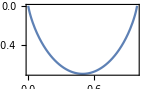
### For a graph y = f(x) -Graphics- it means that—if you pick any two points x_1 and x_2— convexity implies that for every point in the interval between x_1and x_2: :

#### This may be easier to see than read:

#### An important thing about convexity is that is not local: the construction depends on geometry that is not in the proximity of the point (x,f[x]) Why is this important? Suppose that F[x] is the energy of a system with a fixed number of moles—for example, if there is one mole, then we can call the molar energy. Suppose further that x is the molar density of some extensive quantity. In our system, let’s suppose that x is the molar volume . Then is the molar energy as a function of the molar volume. 1) If is not convex then we can find two other molar volumes and (for example, molar volumes of 1/2 and and 3/4) such that the system’s average value is is between and (for example if = 5/8, then half of the system is at and the other half is at ) -Graphics- For the non-convex case, the system can lower its molar energy by separating into a dense and less dense portion such that the average molar volume remains constant. 2) If is convex, then there are no two other molar volumes for which the energy is lower. -Graphics-

## Convexity in higher dimensions

### In the examples above, we were considering the convexity of a graph . The convexity is “from below”. We can also consider the convexity of a surface: {x[u,v],y[u,v],z[u,v]}. In this case, we consider convexity “from without”. Nonconvexity means—that for any point {x,y,z} on the surface—there are other points that can be connected with a plane (instead of a line as above) and part of the plane is “outside” the surface. Convexity means there are no other such points. Spheres and ellipsoids are convex shapes.

#### This is not a convex shape :

```mathematica
Module[{f},
f[θ_,ϕ_]:=(1- Cos[4 θ]/8){Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Cos[ϕ]Sin[ϕ]};
ParametricPlot3D[f[θ,ϕ],{θ,0,2Pi},{ϕ,-Pi/2,Pi}]
]
```

-Graphics3D-

#### The shape can be “convexified” by constructing a convex hull:

```mathematica
Module[
{directions = RandomPoint[Sphere[],1000],thetaPhis,f,points,convexHull},
thetaPhis =Rest/@(ToSphericalCoordinates/@directions);
f[{θ_,ϕ_}]:=(1- Cos[4 θ]/8){Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Cos[ϕ]Sin[ϕ]};
points = f/@thetaPhis;
GraphicsRow[
{
Graphics3D[Point[points],Boxed->False],
ConvexHullMesh[points],
Show[
Graphics3D[Point[points]],
Graphics3D[{Opacity[0.75],ConvexHullMesh[points]},Boxed->False]
]
}
]
]
```

-Graphics-

#### Such convexification is what would be used if the molar energy is a function of two molar densities.

## Convexity under a coordinate transform

### Let’s consider transformation to polar coordinates.

#### WIDGET SOURCE

```mathematica
DynamicModule[
{bg = Plot[x(1-x) + 2/3(x Log[x] + (1-x )Log [1-x]),{x,0,1}, Frame-> True, FrameLabel->{"x","f(x)"}, FrameTicks->None, BaseStyle->{FontSize->18}],
f ,x1,x2},
f[x_]:=x(1-x) + 2/3(x Log[x] + (1-x )Log [1-x]);
Dynamic[
Show[{bg,Graphics[{Point[{Locator[Dynamic[x1,(x1={First[#],f[First[#]]})&]],Locator[Dynamic[x2,(x2={First[#],f[First[#]]})&]]}]}]}],
]
]
```

```mathematica
DynamicModule[{bg = Plot[x(1-x) + 2/3(x Log[x] + (1-x )Log [1-x]),{x,0,1}, Frame-> True, FrameLabel->{"x","f(x)"}, FrameTicks->None, BaseStyle->{FontSize->18}],
f ,points},
f[x_]:=x(1-x) + 2/3(x Log[x] + (1-x )Log [1-x]);
points = {{0.25,f[0.25]},{0.75,f[0.75]}};
LocatorPane[Dynamic[points],
Show[bg,Graphics[
{PointSize[0.05],
Point[Dynamic[{points[[1,1]],f[points[[1,1]]]}]],
Point[Dynamic[{points[[2,1]],f[points[[2,1]]]}]],
Line[{Dynamic[{points[[1,1]],f[points[[1,1]]]}],Dynamic[{points[[2,1]],f[points[[2,1]]]}]}]
}
]
],
Appearance->None
]
]
```

```mathematica
DynamicModule[{f},
f[x_,temp_]:=x(1-x) + temp(x Log[x] + (1-x )Log [1-x]);
Manipulate[
Show[Plot[f[x,temp],{x,0,1}, Frame-> True, FrameLabel->{"x","f(x)"}, FrameTicks->None, BaseStyle->{FontSize->18}],
Graphics[
{PointSize[0.02],
Point[Dynamic[{x1[[1]],f[x1[[1]],temp]}]],
Point[Dynamic[{x2[[1]],f[x2[[1]],temp]}]],
Line[{Dynamic[{x1[[1]],f[x1[[1]],temp]}],Dynamic[{x2[[1]],f[x2[[1]],temp]}]}],
Orange,
Point[Dynamic[{x1[[1]],f[x1[[1]],temp]} +t({x2[[1]],f[x2[[1]],temp] }-{x1[[1]],f[x1[[1]],temp]})]],
Line[{Dynamic[{x1[[1]],f[x1[[1]],temp]} +t({x2[[1]],f[x2[[1]],temp] }-{x1[[1]],f[x1[[1]],temp]})],
Dynamic[{x1[[1]] + t(x2[[1]]-x1[[1]]),f[x1[[1]] + t(x2[[1]]-x1[[1]]),temp] }]
}


]


}
],
SaveDefinitions->True
],
{x1,{0.25,f[0.25,1]},ControlType->Locator,Appearance->None},
{x2,{0.75,f[0.75,1]},ControlType->Locator,Appearance->None},
{{temp,1,Style["Convexity Parameter",16]},0,1},
{{t,0.5,Style["Interpolator",16]},0,1},
Dynamic[Style["Convex: "<>ToString[temp>1/2],{16,Red}]],
Delimiter,
Dynamic[Style["Adjust x1 and x2 by dragging black points",14]]


]
]
```

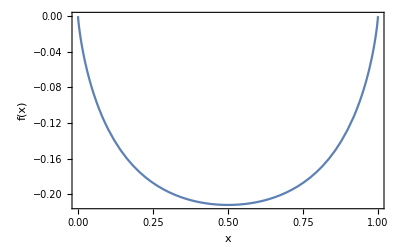

```mathematica
Plot[x(1-x) + 2/3(x Log[x] + (1-x )Log [1-x]),{x,0,1}, Frame-> True, FrameLabel->{"x","f(x)"}, FrameTicks->None, BaseStyle->{FontSize->18}]
```